```mathematica
N[Sqrt[2],100]
```

1.414213562373095048801688724209698078569671875376948073176679737990732478462107038850387534327641573

```mathematica
Expand[(a+b)^5]
```

a^5+5 a^4 b+10 a^3 b^2+10 a^2 b^3+5 a b^4+b^5

```mathematica
Expand[(a+b+c)^7]
```

a^7+7 a^6 b+21 a^5 b^2+35 a^4 b^3+35 a^3 b^4+21 a^2 b^5+7 a b^6+b^7+7 a^6 c+42 a^5 b c+105 a^4 b^2 c+140 a^3 b^3 c+105 a^2 b^4 c+42 a b^5 c+7 b^6 c+21 a^5 c^2+105 a^4 b c^2+210 a^3 b^2 c^2+210 a^2 b^3 c^2+105 a b^4 c^2+21 b^5 c^2+35 a^4 c^3+140 a^3 b c^3+210 a^2 b^2 c^3+140 a b^3 c^3+35 b^4 c^3+35 a^3 c^4+105 a^2 b c^4+105 a b^2 c^4+35 b^3 c^4+21 a^2 c^5+42 a b c^5+21 b^2 c^5+7 a c^6+7 b c^6+c^7

```mathematica
Factor[x^3+6 x^2+11x+6]
```

(1+x) (2+x) (3+x)

```mathematica
Solve[x^3-4 x^2+6x-24==0,x]
```

{{x→4},{x→-ⅈ √6},{x→ⅈ √6}}

```mathematica
Solve[x^4+m x^2+9==0,x]
```

{{x→-(√(-m-√(-36+m^2)))/(√2)},{x→(√(-m-√(-36+m^2)))/(√2)},{x→-(√(-m+√(-36+m^2)))/(√2)},{x→(√(-m+√(-36+m^2)))/(√2)}}

```mathematica
Solve[x+2y+3z==6,2x-3y+2z==14,3x+y-z==-2,{x,y,z}]
```

Solve::bddom: Value {x,y,z} of the domain argument should be Complexes, Reals, Algebraics, Rationals, Integers, Primes, or Automatic.

Solve[x+2 y+3 z==6,2 x-3 y+2 z==14,3 x+y-z==-2,{x,y,z}]

```mathematica
Solve[x+2 y+3 z==6 &&2 x-3 y+2 z==14 &&3 x+y-z==-2,{x,y,z}]
```

{{x→1,y→-2,z→3}}

```mathematica
Solve[x+2y-a z ==0 && b x -4y-z==0,{x,y,z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→-((1-a b) x)/(2 (1+2 a)),z→-((-2-b) x)/(1+2 a)}}

```mathematica
NSolve[x^7-7x+9==0 &&x>=-2 && x<=-1,x]
```

{{x→-1.53101}}

```mathematica
NSolve[Sin[x^2]==x^3 &&x>=0.5 && x<=1,x]
```

{{x→0.895993}}

```mathematica
Limit[(n^100+n^99)^(1/100)-n,n->∞]
```

1/100

```mathematica
Limit[n^2 ((1+p/n)^q-(1+q/n)^p),n->∞]
```

-1/2 p (p-q) q

```mathematica
Limit[2^-n ∏_(k=1)^n (1+k/n),n->∞]
```

0

```mathematica
Limit[(∑_(k=1)^n k^5)/n^6,n->∞]
```

1/6

```mathematica
D[a x^5+(b+1) x^3+7x+1,x]
```

7+3 (1+b) x^2+5 a x^4

```mathematica
D[x^2 Cos[2x],{x,10}]
```

23040 Cos[2 x]-1024 x^2 Cos[2 x]-10240 x Sin[2 x]

```mathematica
23040 Cos[2 0]-1024 0^2 Cos[2 0]-10240 x Sin[2 0]
```

23040

```mathematica
∫x^4/(x^2+1)ⅆx
```

-x+x^3/3+ArcTan[x]

```mathematica
D[Sin[x] Cosh[y],{x,2}]+D[Sin[x] Cosh[y],{y,2}]
```

0

```mathematica
f[x_]:=a x+b/(1+x)
```

```mathematica
D[f[x],x]
```

a-b/(1+x)^2

```mathematica
∫_1^3 f[x]ⅆx
```

4 a+b Log[2]

```mathematica
Series[f[x],{x,a,3}]
```

(a^2+b/(1+a))+(a-b/(1+a)^2) (x-a)+(b (x-a)^2)/(1+a)^3-(b (x-a)^3)/(1+a)^4+O[x-a]^4

```mathematica
Solve[a-b/(1+x)^2==0,x]
```

{{x→(-√a-√b)/(√a)},{x→(-√a+√b)/(√a)}}

```mathematica
f[(-√a-√b)/(√a)]
```

√a (-√a-√b)+b/(1+(-√a-√b)/(√a))

```mathematica
f[(-√a+√b)/(√a)]
```

√a (-√a+√b)+b/(1+(-√a+√b)/(√a))

```mathematica
Limit[f[x],x->-1,Direction->"FromAbove"]
```

b ∞

```mathematica
Limit[f[x],x->-1,Direction->"FromBelow"]
```

b (-∞)

```mathematica
Limit[f[x]/x,x->∞]
```

a

```mathematica
Limit[f[x]-a x,x->∞]
```

0

```mathematica
g[x_]:=1.3 x+12/(1+x)
```

```mathematica
h[x_]:=1.3 x
```

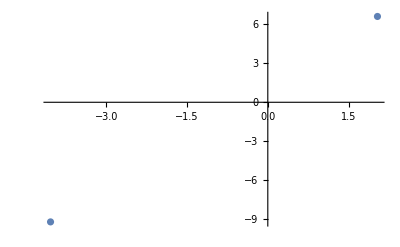

```mathematica
ListPlot[{{(-√1.3-√12)/(√1.3),g[(-√1.3-√12)/(√1.3)]},{(-√1.3+√12)/(√1.3),g[(-√1.3+√12)/(√1.3)]}}]
```

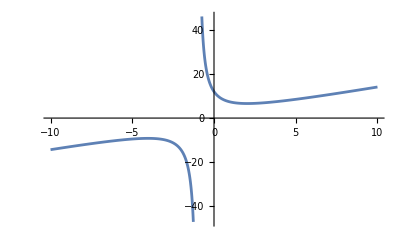

```mathematica
Plot[g[x],{x,-10,10}]
```

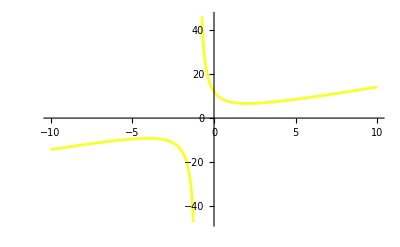

```mathematica
Plot[g[x],{x,-10,10},PlotStyle->RGBColor[0.97,1.,0.17]]
```

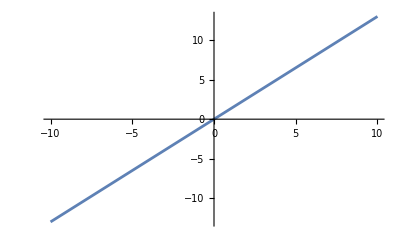

```mathematica
Plot[h[x],{x,-10,10}]
```

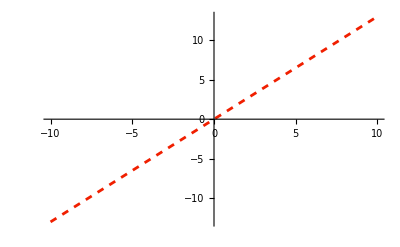

```mathematica
Plot[h[x],{x,-10,10},PlotStyle->Directive[RGBColor[0.9400000000000001,0.12,0.],Dashed]]
```

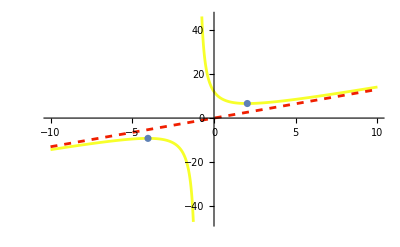

```mathematica
Show[Plot[g[x],{x,-10,10},PlotStyle->RGBColor[0.97,1.,0.17]],Plot[h[x],{x,-10,10},PlotStyle->Directive[RGBColor[0.9400000000000001,0.12,0.],Dashed]],ListPlot[{{(-√1.3-√12)/(√1.3),g[(-√1.3-√12)/(√1.3)]},{(-√1.3+√12)/(√1.3),g[(-√1.3+√12)/(√1.3)]}}]]
```

```mathematica
M={{2,-1,1},{-2,1,2},{-1,-1,4}}
```

{{2,-1,1},{-2,1,2},{-1,-1,4}}

```mathematica
MatrixForm[M]
```

(2 | -1 | 1
-2 | 1 | 2
-1 | -1 | 4)

```mathematica
Det[M]
```

9

```mathematica
Tr[M]
```

7

```mathematica
Transpose[M]
```

{{2,-2,-1},{-1,1,-1},{1,2,4}}

```mathematica
Inverse[M]
```

{{2/3,1/3,-1/3},{2/3,1,-2/3},{1/3,1/3,0}}

```mathematica
Eigensystem[M]
```

{{3,3,1},{{1,0,1},{-1,1,0},{1,2,1}}}

```mathematica
A={{1,1,a},{1,1,a},{1,1,a}}
```

{{1,1,a},{1,1,a},{1,1,a}}

```mathematica
B={{1,1,b},{1,1,b},{1,1,b}}
```

{{1,1,b},{1,1,b},{1,1,b}}

```mathematica
P=A.B
```

{{2+a,2+a,2 b+a b},{2+a,2+a,2 b+a b},{2+a,2+a,2 b+a b}}

```mathematica
Det[P]
```

0

```mathematica
Eigensystem[P]
```

{{0,0,(2+a) (2+b)},{{-b,0,1},{-1,1,0},{1,1,1}}}

WolframAlphaQueryNoResults